```mathematica
Clear["Global`*"];
Off[General::spell];
Off[General::spell1];
```

```mathematica
f[x_]:=16r*(0.5^4-(0.5-x)^4)
```

```mathematica
iterator[m_,n_] := Drop[NestList[f,0.5,n],m]
drawpoint[y_] := Point[{r,y}]
```

```mathematica
graph[rmin_,rmax_, nr_, mdrop_, n_] := 
Graphics[ 
{PointSize[0.001],
Parallelize[Table [
 Map[drawpoint, iterator [mdrop,n ] ], 
{r, rmin, rmax, (rmax-rmin)/nr} ]]}]
```

```mathematica
Show [ 
graph[0, 1, 300, 300, 500], 
Axes -> False, 
Frame -> True, 
FrameLabel -> {"r", "x"}, 
AspectRatio -> 1 ]
```

-Graphics-

```mathematica
Show [ 
graph[0.99, 1, 300, 300, 500], 
Axes -> False, 
Frame -> True, 
FrameLabel -> {"r", "x"}, 
AspectRatio -> 1 ]
```

-Graphics-

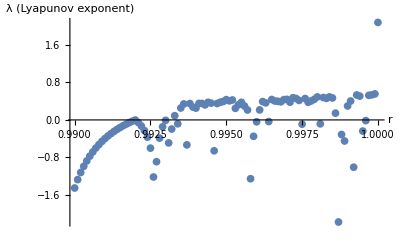

```mathematica
Show[ListPlot[Parallelize[Table[{r,1/2000*Sum[Log[Abs[f'[FixedPoint[f,0.5,i]]]],{i,1,2000}]},{r,Range[0.99,1,0.0001]}]]]
,AxesLabel->{HoldForm[r],HoldForm[λ (Lyapunov exponent)]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```